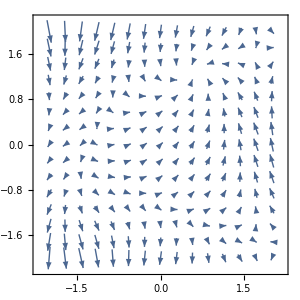
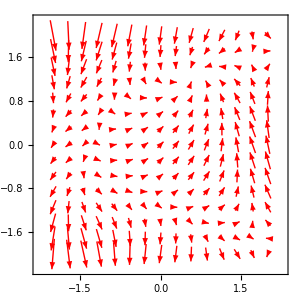

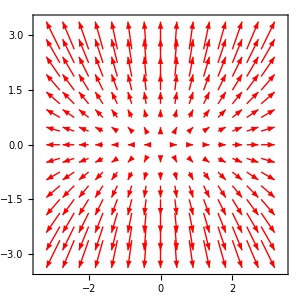
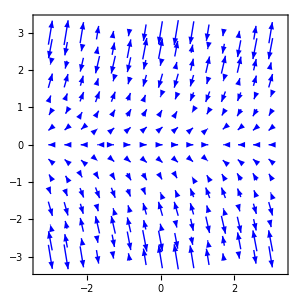

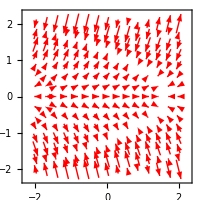
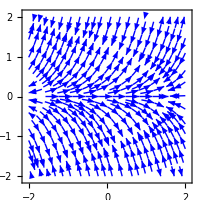
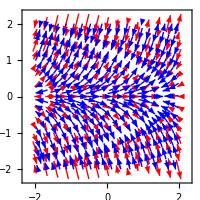

```mathematica
vctFld={Cos[x^2+y],1+x-y^2};
grVctrPl0=VectorPlot[vctFld,{x,-2,2},{y,-2,2},ImageSize->300];
grVctrPl1=VectorPlot[vctFld,{x,-2,2},{y,-2,2},BaseStyle->{12},ImageSize->300,VectorStyle->Red,VectorScale->{0.1,Small,Automatic}];
Row[{grVctrPl0,grVctrPl1},Spacer[20]]
tv51=VectorPlot[Evaluate[D[x^2+2*y^2,{{x,y}}]],{x,-3,3},{y,-3,3},VectorStyle->Red,VectorScale->{0.1,Small,Automatic},BaseStyle->{12},ImageSize->300];
tv52=VectorPlot[Evaluate[D[Sin[x+y^2],{{x,y}}]],{x,-3,3},{y,-3,3},VectorStyle->Blue,VectorScale->{0.08,Small,Automatic},BaseStyle->{12},ImageSize->300];
Row[{tv51,tv52},Spacer[20]]
grf1=VectorPlot[{Cos[x+y^2],2*y*Cos[x+y^2]},{x,-2,2},{y,-2,2},VectorStyle->Red,VectorScale->{0.1,Small,Automatic},BaseStyle->{12},ImageSize->200];
grStrPl1=StreamPlot[{Cos[x+y^2],2*y*Cos[x+y^2]},{x,-2,2},{y,-2,2},StreamStyle->Blue,BaseStyle->{12},ImageSize->200];
grStrPl1a=Show[grf1,grStrPl1];
Row[{grf1,grStrPl1,grStrPl1a},Spacer[5]]
```

```mathematica
Array[#^5+#&,7,4]
StringLength["StreamPoints→11"]
InputForm["Array[#^5+#^1&,7,4]"]
```

{1028,3130,7782,16814,32776,59058,100010}

15

"Array[#^5+#^1&,7,4]"

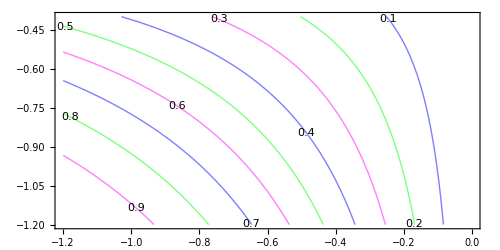

```mathematica
ContourPlot[Sin[x*y],{x,-1.2,0},{y,-1.2,-0.4},AspectRatio->1/2,BaseStyle->14,ImageSize->500,ContourShading->False,ContourLabels->All,ContourStyle->{{Blue,Thick},{Green,Thick},Magenta}]
```

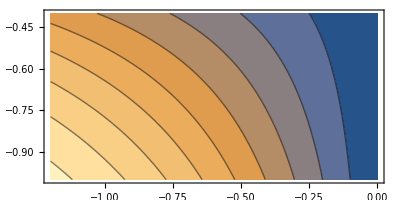
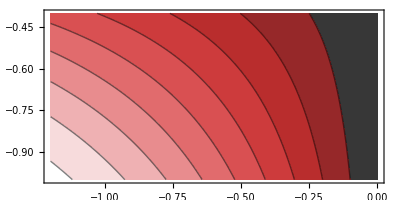

```mathematica
rClrF={"BeachColors","CandyColors","CherryTones","FallColors","LakeColors","MintColors","RoseColors","SolarColors","SunsetColors"};
grC1=ContourPlot[Sin[x*y],{x,-1.2,0},{y,-1.0,-0.4},AspectRatio->1/2,BaseStyle->14,ImageSize->400];
grC2=ContourPlot[Sin[x*y],{x,-1.2,0},{y,-1.0,-0.4},AspectRatio->1/2,BaseStyle->14,ImageSize->400,ColorFunction->rClrF[[3]]]; Row[{grC1,grC2},Spacer[20]]
```

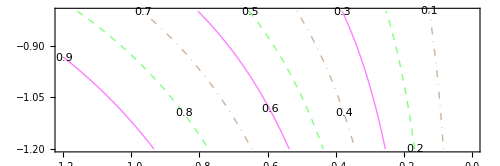

```mathematica
ContourPlot[Sin[x*y],{x,-1.2,0},{y,-1.2,-0.8},AspectRatio->1/3,BaseStyle->14,ImageSize->500,ContourShading->False,ContourLabels->All,ContourStyle->{{Brown,DotDashed},{Green,Dashed}, Magenta}]
```

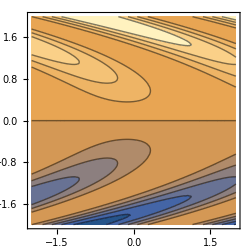
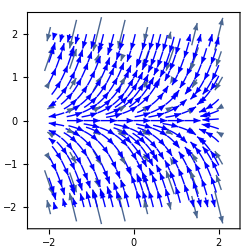

```mathematica
gr2DCP1=ContourPlot[{Cos[x+y^2]*2*y*Cos[x+y^2]},{x,-2,2},{y,-2,2},Contours->10,BaseStyle->{12},ImageSize->250];
gr2DQst=StreamPlot[{Cos[x+y^2],2*y*Cos[x+y^2]},{x,-2,2},{y,-2,2},StreamStyle->Blue,BaseStyle->{12},VectorPoints->8,ImageSize->250];
Row[{gr2DCP1,gr2DQst},Spacer[10]]
```

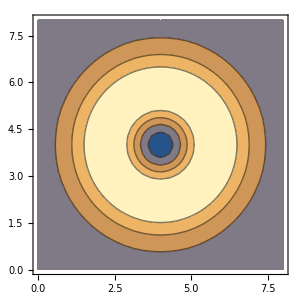
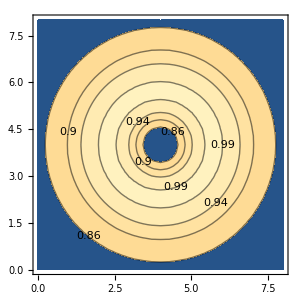

```mathematica
fXY[x_,y_]:=Sin[1+1.2*E^(-(x/2-2)^2-(y/2-2)^2)];
grXY1=ContourPlot[fXY[x,y],{x,0,8},{y,0,8},ImageSize->300,Contours->4];
grXY2=ContourPlot[fXY[x,y],{x,0,8},{y,0,8},ImageSize->300,Contours->{0.99,0.89,0.99,0.86},ContourLabels->All]; Row[{grXY1,grXY2},Spacer[20]]
```

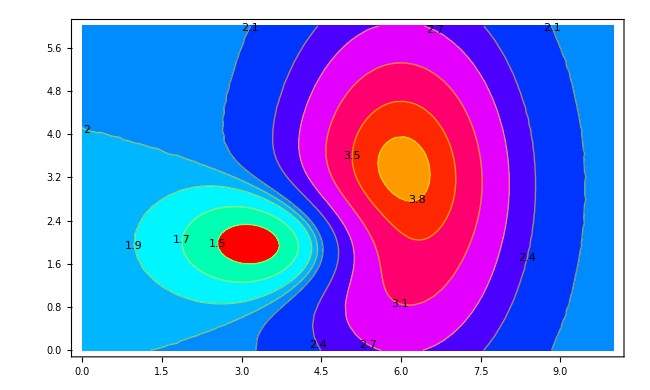

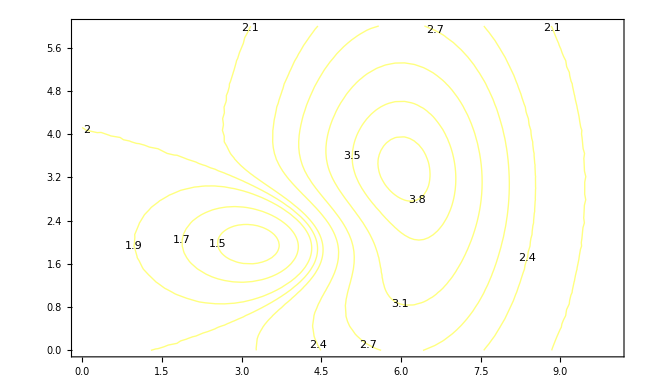

```mathematica
xmin:=0;xmax:=10;ymin:=0;ymax:=6;
fXY[x_,y_]:=2-E^(-(x/2-2)^2-(y-2)^2)+2*E^(-(x/2-3)^2-(y/3-1)^2);
aspRat=(ymax-ymin)/(xmax-xmin);
zIzl={1.5,1.7,1.9,2.,2.1,2.4,2.7,3.1,3.5,3.8};
nIzl=Dimensions[zIzl];
cLr0=0;cLrStep=(nIzl+1)/nIzl;
grCont0=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->zIzl,ContourStyle->Directive[Thick,Yellow],ContourLabels->True,ColorFunction->(Hue[cLr0+cLrStep*#1]&),AspectRatio->aspRat,ImageSize->650]

(*также выводим карту только изолиний,чтобы далее использовать и визуализировать исходные...*)
grCont1=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->zIzl,ContourStyle->Directive[Thick,Yellow],ContourLabels->True,ContourShading->False,AspectRatio->aspRat,ImageSize->650]
```

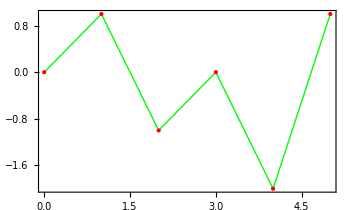
-Graphics--Graphics-

```mathematica
lstForGr={{0,0},{1,1},{2,-1},{3,0},{4,-2},{5,1}};
gr2DLi1=Graphics[{Green,Line[lstForGr],Red,Point[lstForGr]},Frame->True,ImageSize->350];
gr2DLi2=Graphics[{Magenta,BSplineCurve[lstForGr],Green,Line[lstForGr],Red,Point[lstForGr]},Frame->True,ImageSize->350];
Row[{gr2DLi1,gr2DLi2},Spacer[10]]
```

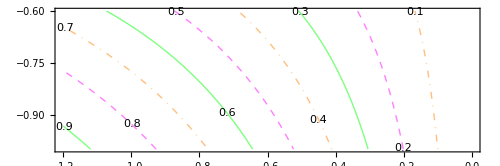

```mathematica
ContourPlot[Sin[x*y],{x,-1.2,0},{y,-1.0,-0.6},AspectRatio->1/3,BaseStyle->14,ImageSize->500,ContourShading->False,ContourLabels->All,ContourStyle->{{Orange,DotDashed},{Magenta,Dashed}, Green}]
```

```mathematica
StringLength["ContourStyle→{{Orange,DotDashed},{Magenta,Dashed}"]
```

49

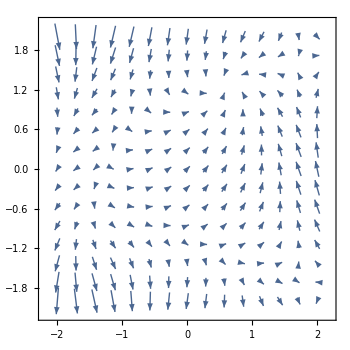
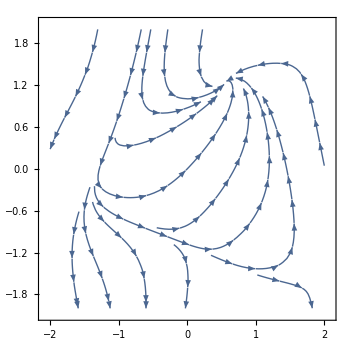

```mathematica
Clear[x,y]
vctFld={Cos[x^2+y],1+x-y^2};
grVect1=VectorPlot[vctFld,{x,-2,2},{y,-2,2},ImageSize->350];
grVect2=StreamPlot[vctFld,{x,-2,2},{y,-2,2},StreamPoints->15,ImageSize->350];
Row[{grVect1,grVect2},Spacer[20]]
```

```mathematica
CandlestickChart[dEPAMClose,ImageSize->500]
```

CandlestickChart::ldata: dEPAMClose is not a valid dataset or list of datasets.

CandlestickChart[dEPAMClose,ImageSize→500]

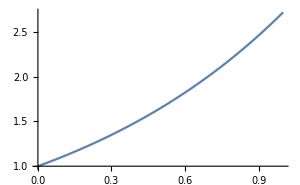
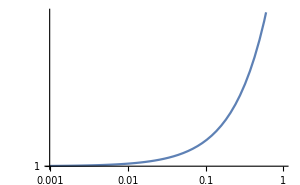

```mathematica
fnh[x_]:=Exp[x]
Row[{Plot[fnh[x],{x,0,1},ImageSize->300],LogLogPlot[fnh[x],{x,0,1},ImageSize->300]},Spacer[10]]
```

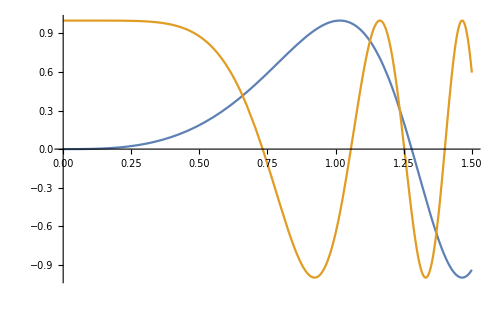

```mathematica
aX="X";
aY="f1,f2";
f1[x_]:=Sin[1.5*x^3];
f2[x_]:=Cos[4*x^3];
grf1=Plot[{f1[x],f2[x]},{x,0,3/2},ImageSize->500,BaseStyle->16,AxesStyle->{True,Arrowheads[0.05]}]
```

```mathematica
DayCount[{1907,11,14},"Today"]
```

DayCount::date: Expression Today cannot be interpreted as a date specification.

DayCount[{1907,11,14},Today]

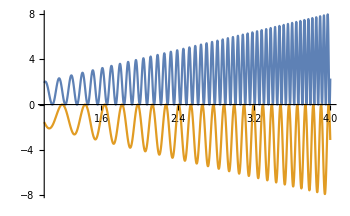
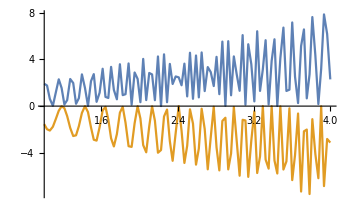

```mathematica
grf1=Plot[{x+x*Sin[20*x^2],x*Sin[10*x^2]-x},{x,1,4},BaseStyle->15,ImageSize->350];
grf2=Plot[{x+x*Sin[20*x^2],x*Sin[10*x^2]-x},{x,1,4},BaseStyle->15,ImageSize->350,MaxRecursion->1];
Row[{grf1,grf2},Spacer[15]]
```

```mathematica
Clear[a,b,c,d,w,fRab];
fRab:=Tan[w]+a*b+b*w^3-c/(d+w)+w/(d+w)
Part[]
```

a b+b w^3-c/(d+w)+w/(d+w)+Tan[w]

```mathematica
abc="Степень_n"
Manipulate[Sum[k^n,{k,0,m}],{{n,1},30,1}]
```

Степень_n

```mathematica
DayName[{1907,14,11}]
```

Tuesday

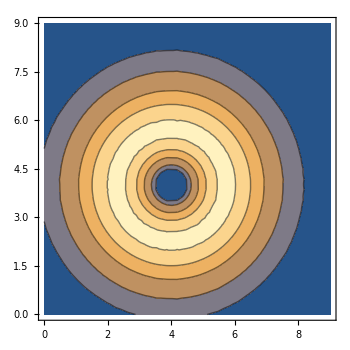
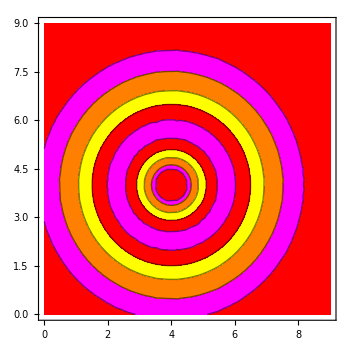

```mathematica
fXY[x_,y_]:=Sin[1+1.2*E^(-(x/2-2)^2-(y/2-2)^2)];
grXY1=ContourPlot[fXY[x,y],{x,0,9},{y,0,9},Contours->{0.85,0.87,0.91,0.95,0.99},ImageSize->350];
grXY2=ContourPlot[fXY[x,y],{x,0,9},{y,0,9},Contours->{0.85,0.87,0.91,0.95,0.99},ContourShading->{Red,Magenta,Orange,Yellow},ImageSize->350];
Row[{grXY1,grXY2},Spacer[20]]
```

```mathematica
Clear[a,b,c,d,z];
fRab:=a*z+b*z^2-c/(d+z)+z/(d+z)+Cos[z];
fRab
Part[fRab,{2,3,5}]//InputForm
```

a z+b z^2-c/(d+z)+z/(d+z)+Cos[z]

b*z^2 - c/(d + z) + Cos[z]

```mathematica
ImageSize->350,Row[{grR1,grR2},Spacer[10]],dCh={{{2,3},{5,7},{3,4},{7,5},{4,3}},{{4,2},{7,5},{4,3},{2,6},{7,5}}};
```

```mathematica
PlotTheme
```